# Quantum Decoherence

```mathematica
Quit[]
```

```mathematica
Needs["QuantumMob`Q3`"]
```

```mathematica
Let[Qubit,S]
```

The following definition is used frequently through out this workbook, and we put it here. The function kraus constructs the Kraus elements from the unitary representation of the quantum operation. Here U is the unitary operator on the total system (system plus environment) and init is the initial (pure) state of the environment. The system and environment are assumed to be initially in a product state.

```mathematica
$d=3;
kraus[U_?MatrixQ,init_?VectorQ]:=Map[kraus[U,init,#]&,Range[$d]]
kraus[U_?MatrixQ,init_?VectorQ,k_Integer]:=PartialTrace[
U.CircleTimes[One[$d],Dyad[init,UnitVector[$d,k]]],
{$d,$d},{2}];
```

"Table of Contents"

## How Does Decoherence Occur?

Consider a quantum circuit model equivalent to the Mach-Zehnder interferometer.

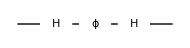

```mathematica
qc=QuantumCircuit[Ket[S@{1}],S[1,6],Phase[ϕ,S[1,3],"Label"->"ϕ"],S[1,6]]
```

```mathematica
out=Elaborate[qc]
```

1/2 (1+ⅇ^(ⅈ ϕ)) 0_(,,S_(,,1))+1/2 (1-ⅇ^(ⅈ ϕ)) 1_(,,S_(,,1))

```mathematica
Let[Real,ϕ]
{P[0,ϕ_],P[1,ϕ_]}=Abs[Normal@Matrix@out]^2//Elaborate//ExpToTrig//Simplify
```

{Cos[ϕ/2]^2,Sin[ϕ/2]^2}

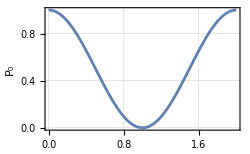

```mathematica
Plot[P[0,Pi s],{s,0,2},FrameLabel->{"ϕ / π","P_0"}]
```

Consider a quantum circuit model equivalent to the Mach-Zehnder interference experiment with a two-level system coupled to one of the two arms.

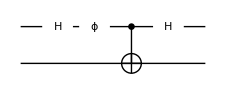

```mathematica
qc=QuantumCircuit[Ket[S@{1,2}],S[1,6],Phase[ϕ,S[1,3],"Label"->"ϕ"],CNOT[S[1],S[2]],S[1,6]]
```

```mathematica
out=Elaborate[qc]
```

1/2 0_(,,S_(,,1))0_(,,S_(,,2))+1/2 ⅇ^(ⅈ ϕ) 0_(,,S_(,,1))1_(,,S_(,,2))+1/2 1_(,,S_(,,1))0_(,,S_(,,2))-1/2 ⅇ^(ⅈ ϕ) 1_(,,S_(,,1))1_(,,S_(,,2))

```mathematica
Let[Real,ϕ]
rho=PartialTrace[out,S[2]]
```

1/2

Now, consider a quantum circuit model equivalent to the Mach-Zehnder interference experiment with a two-level system weakly coupled to one of the two arms. Here we assume the unitary operator U=U_y(θ) with θ<π acting conditionally on the two-level system.

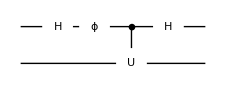

```mathematica
qc=QuantumCircuit[Ket[S@{1,2}],S[1,6],Phase[ϕ,S[1,3],"Label"->"ϕ"],ControlledGate[S[1],Rotation[θ,S[2,2]],"Label"->"U"],S[1,6]]
```

The final state is an entangled state in general.

```mathematica
out=Elaborate[qc]//Simplify
```

1/2 ((1+ⅇ^(ⅈ ϕ) Cos[θ/2]) 0_(,,S_(,,1))0_(,,S_(,,2))+(1-ⅇ^(ⅈ ϕ) Cos[θ/2]) 1_(,,S_(,,1))0_(,,S_(,,2))+ⅇ^(ⅈ ϕ) (0_(,,S_(,,1))1_(,,S_(,,2))-1_(,,S_(,,1))1_(,,S_(,,2))) Sin[θ/2])

However, the entanglement is not a maximally entangled state. The density operator for the photon manifests coherence to certain extent.

```mathematica
Let[Real,ϕ,θ]
rho=PartialTrace[out,S[2]]//ExpToTrig//Elaborate
```

1/2+1/2 Cos[θ/2] Cos[ϕ] S_(,,1)^(,,Z)-1/2 Cos[θ/2] S_(,,1)^(,,Y) Sin[ϕ]

```mathematica
{P[0,θ_,ϕ_],P[1,θ_,ϕ_]}=ExpToTrig@Diagonal@Matrix@rho
```

{1/2+1/2 Cos[θ/2] Cos[ϕ],1/2-1/2 Cos[θ/2] Cos[ϕ]}

Depending on the strength of the coupling, the interference may survive partially.

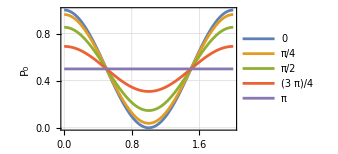

```mathematica
tt=Range[0,4]Pi/4;
Plot[Evaluate[P[0,#,Pi s]&/@tt],{s,0,2},
FrameLabel->{"ϕ / π","P_0"},PlotLegends->tt]
```

## Quantum Operations

### Kraus Representation

We consider a chain of three qubits. The first qubit is regarded as the “system”, and the other two form the “environment”.

```mathematica
$L=3;
jj=Range[$L];
sys=1;
env=Range[2,$L];
```

Here is the Hamiltonian describing the chain. We are measuring the energy in units of B (B=1).

```mathematica
Let[Real,J]
H=S[sys,3]/2+J/2* Total[ChainBy[S[jj,1],Multiply]]
```

1/2 J (S_(,,1)^(,,X)S_(,,2)^(,,X)+S_(,,2)^(,,X)S_(,,3)^(,,X))+1/2 S_(,,1)^(,,Z)

The system has a discrete symmetry. It is invariant under the rotation around the z-axis by angle π.

```mathematica
V=Rotation[Pi,S[1,3]]**Rotation[Pi,S[2,3]]**Rotation[Pi,S[3,3]]//Elaborate
V**H**Dagger[V]//Elaborate
```

ⅈ S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,Z)

1/2 J S_(,,1)^(,,X)S_(,,2)^(,,X)+1/2 J S_(,,2)^(,,X)S_(,,3)^(,,X)+1/2 S_(,,1)^(,,Z)

The symmetry leads to the degeneracy of the eigenvalues of the Hamiltonian.

```mathematica
ProperValues[H]
```

{1/2 (-J-√(1+J^2)),1/2 (-J-√(1+J^2)),1/2 (J-√(1+J^2)),1/2 (J-√(1+J^2)),1/2 (-J+√(1+J^2)),1/2 (-J+√(1+J^2)),1/2 (J+√(1+J^2)),1/2 (J+√(1+J^2))}

The time-evolution operator of the chain is evaluated.

```mathematica
Let[Real,t]
U[t_]=Elaborate@MultiplyExp[-I t H];
```

We suppose that the chain is initially in the state L⊗L⊗L, where L=(0+i1)/√2.

```mathematica
Clear[vec]
vec[0]=ProductState[S@jj->{1,I}/Sqrt[2]]
vec[t_]=U[t]**Elaborate[vec[0]];
```

(0/(√2)+(ⅈ 1)/(√2))_(S_(,,1))⊗(0/(√2)+(ⅈ 1)/(√2))_(S_(,,2))⊗(0/(√2)+(ⅈ 1)/(√2))_(S_(,,3))

Here is a set of replacement rules to be used later to simplify expressions.

```mathematica
rules={Sqrt[1+J^2]->Ω,1/Sqrt[1+J^2]->1/Ω}
```

{√(1+J^2)→Ω,1/(√(1+J^2))→1/Ω}

```mathematica
Clear[rho]
rho[t_]=PartialTrace[vec[t],S@env]//Elaborate//ExpToTrig//Garner;
rho[t]/.rules
```

1/2+1/2 Cos[t Ω] S_(,,1)^(,,Y)-(S_(,,1)^(,,X) Sin[t Ω])/(2 Ω)

Take a look at the dynamical evolution of the state of the “system” (the first qubit), after tracing out the “environment” (the other two qubits). On the left, shown is the evolution in the absence of the coupling to the environment. On the right, the evolution is not coherent due to the coupling to the environment. The evolution is still periodic because the environment is finite.

```mathematica
bv0=Block[{J=0.},Table[BlochVector[rho[2Pi*t]],{t,0,5,0.2}]];
bv=Block[{J=.5},Table[BlochVector[rho[2Pi*t]],{t,0,5/J,0.2}]];
GraphicsRow@{BlochSphere[{Blue,Bead/@bv0}],BlochSphere[{Red,Bead/@bv}]}
```

-Graphics-

Now, let us examine the evolution in terms of the supermap. This is the initial state of the system.

```mathematica
in=Elaborate@ProductState[S[sys]->{1,I}/Sqrt[2]];
in=Elaborate@Dyad[in,in,S[1]]
```

1/2+1/2 S_(,,1)^(,,Y)

To find the Kraus elements, consider the initial state of the environment.

```mathematica
sgm=Elaborate@ProductState[S@env->{1,I}/Sqrt[2]]
```

1/2 0_(,,S_(,,2))0_(,,S_(,,3))+1/2 ⅈ 0_(,,S_(,,2))1_(,,S_(,,3))+1/2 ⅈ 1_(,,S_(,,2))0_(,,S_(,,3))-1/2 1_(,,S_(,,2))1_(,,S_(,,3))

Finally, this is the Kraus elements of the quantum operation.

```mathematica
bs=Basis[S@env];
prj=Map[Dyad[sgm,#,S@env]&,bs];
ops=U[t]**prj//Elaborate;
```

```mathematica
kraus=PartialTrace[#,S@env]&/@ops//ExpToTrig//Elaborate//Garner;
kraus/.rules
```

{1/2 Cos[(t Ω)/2] (Cos[(J t)/2]+ⅈ Sin[(J t)/2])+(J S_(,,1)^(,,X) (Cos[(J t)/2]-ⅈ Sin[(J t)/2]) Sin[(t Ω)/2])/(2 Ω)+(S_(,,1)^(,,Z) (-ⅈ Cos[(J t)/2]+Sin[(J t)/2]) Sin[(t Ω)/2])/(2 Ω),1/2 Cos[(t Ω)/2] (ⅈ Cos[(J t)/2]+Sin[(J t)/2])+(S_(,,1)^(,,Z) (Cos[(J t)/2]-ⅈ Sin[(J t)/2]) Sin[(t Ω)/2])/(2 Ω)+(ⅈ J S_(,,1)^(,,X) (Cos[(J t)/2]+ⅈ Sin[(J t)/2]) Sin[(t Ω)/2])/(2 Ω),1/2 Cos[(t Ω)/2] (ⅈ Cos[(J t)/2]+Sin[(J t)/2])+(S_(,,1)^(,,Z) (Cos[(J t)/2]-ⅈ Sin[(J t)/2]) Sin[(t Ω)/2])/(2 Ω)+(J S_(,,1)^(,,X) (-ⅈ Cos[(J t)/2]+Sin[(J t)/2]) Sin[(t Ω)/2])/(2 Ω),-1/2 Cos[(t Ω)/2] (Cos[(J t)/2]+ⅈ Sin[(J t)/2])+(J S_(,,1)^(,,X) (Cos[(J t)/2]-ⅈ Sin[(J t)/2]) Sin[(t Ω)/2])/(2 Ω)+(ⅈ S_(,,1)^(,,Z) (Cos[(J t)/2]+ⅈ Sin[(J t)/2]) Sin[(t Ω)/2])/(2 Ω)}

```mathematica
Clear[new]
new[t_]=Elaborate@Supermap[kraus][in];
new[t]/.rules
```

1/2+1/2 Cos[t Ω] S_(,,1)^(,,Y)-(S_(,,1)^(,,X) Sin[t Ω])/(2 Ω)

```mathematica
new[t]-rho[t]//Elaborate//Garner
```

0

### Choi Isomorphism

### Unitary Representation

### Examples

The phase damping process is specified by two Kraus elements.

```mathematica
Let[Real,p]
ops={Sqrt[(1+Sqrt[1-p])/2],Sqrt[(1-Sqrt[1-p])/2]*S[3]};
spr=Supermap[ops]
```

Supermap[…]

Here p is the probability for the phase to be flipped.

```mathematica
Let[Real,ρ]
rho=1/2+ρ[{1,2,3}].S[All]
```

1/2+S^X ρ_(,,1)+S^Y ρ_(,,2)+S^Z ρ_(,,3)

The supermap transforms the above density operator as follows.

```mathematica
new=spr[rho]
```

1/2+√(1-p) S^X ρ_(,,1)+√(1-p) S^Y ρ_(,,2)+S^Z ρ_(,,3)

The amplitude damping process is specified by two Kraus elements.

```mathematica
Let[Real,p]
ops={S[10]+Sqrt[1-p]*S[11],Sqrt[p]*S[4]};
spr=Supermap[ops]
```

Supermap[…]

Here p is the probability for the phase to be flipped.

```mathematica
Let[Real,ρ]
rho=1/2+ρ[{1,2,3}].S[All]
```

1/2+S^X ρ_(,,1)+S^Y ρ_(,,2)+S^Z ρ_(,,3)

The supermap transforms the above density operator as follows.

```mathematica
new=spr[rho]//Elaborate
```

1/2+√(1-p) S^X ρ_(,,1)+√(1-p) S^Y ρ_(,,2)+S^Z (p (1/2-ρ_(,,3))+ρ_(,,3))

The depolarizing process is specified by three Kraus elements.

```mathematica
Let[Real,p]
ops=Prepend[Sqrt[p/3]*S[All],Sqrt[1-p]];
spr=Supermap[ops]
```

Supermap[…]

Here p is the probability for the phase to be flipped.

```mathematica
Let[Real,ρ]
rho=1/2+ρ[{1,2,3}].S[All]
```

1/2+S^X ρ_(,,1)+S^Y ρ_(,,2)+S^Z ρ_(,,3)

The supermap transforms the above density operator as follows.

```mathematica
new=spr[rho]
```

1/2+(1-(4 p)/3) S^X ρ_(,,1)+(1-(4 p)/3) S^Y ρ_(,,2)+(1-(4 p)/3) S^Z ρ_(,,3)

## Measurements as Quantum Operations

## Quantum Master Equations

### Derivation

### Examples

### Solution Methods

Consider the Lindblad equation for a single-qubit system with the effective Hamiltonian and the Lindblad operators as following:

```mathematica
Let[Real,Ω,Δ,Γ]
```

```mathematica
opH=Δ S[1]/2+Ω S[3]/2
opL={Sqrt[Γ["+"]]S[4],Sqrt[Γ["-"]]S[5]}
```

1/2 Δ S^X+1/2 Ω S^Z

{S^+ √(Γ_(,,+)),S^- √(Γ_(,,-))}

This is the naive form of the generator matrix corresponding to the Lindblad equation without taking into account the Hermicity condition and the probability conservation condition.

```mathematica
mat=ChoiMatrix@LindbladSupermap[opH,opL];
mat=ArrayReshape[Transpose[mat,2<->3],{4,4}];
mat//MatrixForm
```

(-ⅈ (Ω/2-1/2 ⅈ Γ_(,,-))+ⅈ (Ω/2+1/2 ⅈ Γ_(,,-)) | (ⅈ Δ)/2 | -(ⅈ Δ)/2 | Γ_(,,+)
(ⅈ Δ)/2 | -ⅈ (Ω/2-1/2 ⅈ Γ_(,,-))+ⅈ (-Ω/2+1/2 ⅈ Γ_(,,+)) | 0 | -(ⅈ Δ)/2
-(ⅈ Δ)/2 | 0 | ⅈ (Ω/2+1/2 ⅈ Γ_(,,-))-ⅈ (-Ω/2-1/2 ⅈ Γ_(,,+)) | (ⅈ Δ)/2
Γ_(,,-) | -(ⅈ Δ)/2 | (ⅈ Δ)/2 | -ⅈ (-Ω/2-1/2 ⅈ Γ_(,,+))+ⅈ (-Ω/2+1/2 ⅈ Γ_(,,+)))

```mathematica
ρ[1,1]=z;
ρ[1,2]=x+I y;
ρ[2,1]=x-I y;
ρ[2,2]=1-ρ[1,1];
rho=Flatten@Array[ρ,{2,2}];
```

```mathematica
expr=mat.rho
dv=Coefficient[#,{z,x,y}]&/@expr
```

{-1/2 ⅈ (x-ⅈ y) Δ+1/2 ⅈ (x+ⅈ y) Δ+z (-ⅈ (Ω/2-1/2 ⅈ Γ_(,,-))+ⅈ (Ω/2+1/2 ⅈ Γ_(,,-)))+(1-z) Γ_(,,+),-1/2 ⅈ (1-z) Δ+(ⅈ z Δ)/2+(x+ⅈ y) (-ⅈ (Ω/2-1/2 ⅈ Γ_(,,-))+ⅈ (-Ω/2+1/2 ⅈ Γ_(,,+))),1/2 ⅈ (1-z) Δ-(ⅈ z Δ)/2+(x-ⅈ y) (ⅈ (Ω/2+1/2 ⅈ Γ_(,,-))-ⅈ (-Ω/2-1/2 ⅈ Γ_(,,+))),1/2 ⅈ (x-ⅈ y) Δ-1/2 ⅈ (x+ⅈ y) Δ+z Γ_(,,-)+(1-z) (-ⅈ (-Ω/2-1/2 ⅈ Γ_(,,+))+ⅈ (-Ω/2+1/2 ⅈ Γ_(,,+)))}

{{-Γ_(,,-)-Γ_(,,+),0,-Δ},{ⅈ Δ,-ⅈ Ω-(Γ_(,,-))/2-(Γ_(,,+))/2,Ω-1/2 ⅈ Γ_(,,-)-1/2 ⅈ Γ_(,,+)},{-ⅈ Δ,ⅈ Ω-(Γ_(,,-))/2-(Γ_(,,+))/2,Ω+1/2 ⅈ Γ_(,,-)+1/2 ⅈ Γ_(,,+)},{Γ_(,,-)+Γ_(,,+),0,Δ}}

```mathematica
matK={dv[[1]],
(dv[[2]]+dv[[3]])/2,
-(dv[[2]]-dv[[3]])/2}//Simplify;
matK//MatrixForm
```

(-Γ_(,,-)-Γ_(,,+) | 0 | -Δ
0 | 1/2 (-Γ_(,,-)-Γ_(,,+)) | Ω
-ⅈ Δ | ⅈ Ω | 1/2 ⅈ (Γ_(,,-)+Γ_(,,+)))

```mathematica
off={expr[[1]],(expr[[2]]+expr[[3]])/2,I(expr[[2]]-expr[[3]])/2}/.{z->0,x->0,y->0}
```

{Γ_(,,+),0,Δ/2}

Let us consider a single qubit, and examine a master equation. We assume that the system is initially prepared in a pure state (0+1)/√2.

```mathematica
init=(1+S[1])/2;
init//MatrixForm
```

1/2 (1+S^X)

This is the effective Hamiltonian.

```mathematica
opH=S[3];
```

These are the Lindblad operators.

```mathematica
Let[Real,Γ]
opL={Sqrt[Γ["+"]] S[4],Sqrt[Γ["-"]]S[5]}
```

{S^+ √(Γ_(,,+)),S^- √(Γ_(,,-))}

This is the Lindblad basis we are going to use. It happens to be equivalent to the basis consisting of the Pauli operators.

```mathematica
lbs=Elaborate@LieBasis[S]
MatrixForm/@(Matrix[#,S]&)/@lbs
```

{1/(√2),S^X/(√2),S^Y/(√2),S^Z/(√2)}

{(1/(√2) | 0
0 | 1/(√2)),(0 | 1/(√2)
1/(√2) | 0),(0 | -ⅈ/(√2)
ⅈ/(√2) | 0),(1/(√2) | 0
0 | -1/(√2))}

Here are the generator matrix K and the inhomogeneous term when the Lindblad equation is written in the standard form of an inhomogeneous first-order differential equation.

```mathematica
{mat,vec}=LindbladConvert[opH,opL];
mat//SimplifyThrough//MatrixForm
vec//SimplifyThrough//MatrixForm
```

(1/2 (-Γ_(,,-)-Γ_(,,+)) | -2 | 0
2 | 1/2 (-Γ_(,,-)-Γ_(,,+)) | 0
0 | 0 | -Γ_(,,-)-Γ_(,,+))

(0
0
(-Γ_(,,-)+Γ_(,,+))/(√2))

This solves the differential equation based on the generator matrix K and the inhomogeneous term.

```mathematica
Clear[ρ]
ρ[t_]=Block[
{Γ,ρ},
Γ["+"]=.3;
Γ["-"]=.7;
Elaborate@LindbladSolve[opH,opL,init,t]//Chop
];
ρ[t]//MatrixForm
```

0.5+0.5 ⅇ^(-0.5 t) Cos[2. t] S^X+(-0.2+0.2 ⅇ^(-1. t)) S^Z+0.5 ⅇ^(-0.5 t) S^Y Sin[2. t]

To investigate the physical properties of the solution, we calculate the expectation values of the Pauli operators.

```mathematica
{avgX[t_],avgY[t_],avgZ[t_]}=Coefficient[ρ[t],#]&/@S@{1,2,3}
```

{0.5 ⅇ^(-0.5 t) Cos[2. t],0.5 ⅇ^(-0.5 t) Sin[2. t],-0.2+0.2 ⅇ^(-1. t)}

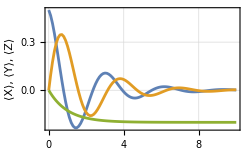

```mathematica
data=Transpose@Table[
{{t,avgX[t]},{t,avgY[t]},{t,avgZ[t]}},
{t,0,10,0.1}
];
ListLinePlot[data,
FrameLabel->{"B_z t","⟨X⟩, ⟨Y⟩, ⟨Z⟩"}
]
```

Consider a three-level atom with the Λ-type level structure.

```mathematica
Let[Qudit,A]
```

In the interaction picture, the Hamiltonian looks like this. We have put the two Rabi transition amplitudes to 1.

```mathematica
opH=(1/10)A[1->1]+(2/10)A[2->2]+A[2->0]+A[0->2]+A[2->1]+A[1->2];
matH=Matrix[opH];
matH//MatrixForm
```

(0 | 0 | 1
0 | 1/10 | 1
1 | 1 | 1/5)

```mathematica
Let[Real,Γ]
opL={
Sqrt[Γ[0,"-"]]*A[2->0],
Sqrt[Γ[0,"+"]]*A[0->2],
Sqrt[Γ[1,"-"]]*A[2->1],
Sqrt[Γ[1,"+"]]*A[1->2]}
matL=Matrix[opL];
MatrixForm/@matL
```

{02 √(Γ_(,,0-)),20 √(Γ_(,,0+)),12 √(Γ_(,,1-)),21 √(Γ_(,,1+))}

{(0 | 0 | √(Γ_(,,0-))
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
√(Γ_(,,0+)) | 0 | 0),(0 | 0 | 0
0 | 0 | √(Γ_(,,1-))
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
0 | √(Γ_(,,1+)) | 0)}

```mathematica
EchoTiming[
ρ[t_]=Block[
{Γ,init},
Γ[0,"-"]=0.05;
Γ[0,"+"]=0.01;
Γ[1,"-"]=0.025;
Γ[1,"+"]=0.005;
init=DiagonalMatrix[{0,1,0}];
LindbladSolve[matH,matL,init,t]
];
]
```

1.31402

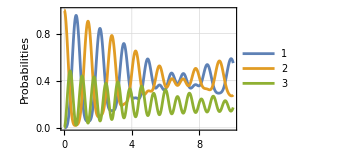

```mathematica
Plot[Evaluate@Diagonal@ρ[t Pi],{t,0,10},
FrameLabel->{"Ω t / π","Probabilities"},
PlotRange->All,
PlotLegends->Automatic]
```

### Examples Revisited

Consider the phase damping process.

It is governed by a single parameter.

```mathematica
Let[Real,γ]
```

The Lindblad generator is specified by a single Lindblad operator. Note that in this case, the effective Hamiltonian vanishes.

```mathematica
ops={Sqrt[γ]/2 S[3]};
gnr=LindbladSupermap[0,ops]
```

LindbladSupermap[…]

We assume that the system is initially prepared in a pure state.

```mathematica
vec=EulerRotation[{0,Pi/4,0},S]**Ket[]
init=ExpressionFor[Matrix@Dyad[vec,vec,S],S]//Elaborate;
```

Cos[π/8] 0_(,,S)+1_(,,S) Sin[π/8]

This is the solution of the Lindblad equation.

```mathematica
Clear[rho]
rho[t_]=LindbladSolve[0,ops,init,t]
```

1/2+S^Z/(2 √2)+(ⅇ^(-(t γ)/2) S^+)/(2 √2)+(ⅇ^(-(t γ)/2) S^-)/(2 √2)

As you can see, the time dependence is governed by γt. This indicates that the system has a single time scale, and it is governed by γ. It is thus convenient to use 1/γ as the unit of time. It is equivalent to put γ=1.

```mathematica
γ=1;
```

```mathematica
data=Table[Chop@BlochVector[rho[s Pi]],{s,0,3,0.1}];
BlochSphere[{Red,Bead/@data}]
```

-Graphics3D-

Consider the amplitude damping process.

It is governed by a single parameter.

```mathematica
Let[Real,γ]
```

The Lindblad generator is specified by a single Lindblad operator. In this case, the effective Hamiltonian vanishes.

```mathematica
ops={Sqrt[γ]*S[4]};
gnr=LindbladSupermap[0,ops]
```

LindbladSupermap[…]

We assume that the system is initially prepared in a pure state.

```mathematica
vec=EulerRotation[{0,Pi/4,0},S]**Ket[]
init=ExpressionFor[Matrix@Dyad[vec,vec,S],S]//Elaborate;
```

Cos[π/8] 0_(,,S)+1_(,,S) Sin[π/8]

This is the solution of the Lindblad equation.

```mathematica
rho[t_]=LindbladSolve[0,ops,init,t]
```

1/2+1/4 ⅇ^(-t γ) (-2+√2+2 ⅇ^(t γ)) S^Z+(ⅇ^(-(t γ)/2) S^+)/(2 √2)+(ⅇ^(-(t γ)/2) S^-)/(2 √2)

As you can see, the time dependence is governed by γt. This indicates that the system has a single time scale, and it is governed by γ. It is thus convenient to use 1/γ as the unit of time. It is equivalent to put γ=1.

```mathematica
γ=1;
```

```mathematica
data=Table[Chop@BlochVector[rho[s Pi]],{s,0,3,0.1}];
BlochSphere[{Red,Bead/@data}]
```

-Graphics3D-

Consider the depolarizing process.

It is governed by a single parameter.

```mathematica
Let[Real,γ]
```

The Lindblad generator is specified by three Lindblad operators. In this case, the effective Hamiltonian vanishes.

```mathematica
ops=Sqrt[γ/3]*S[All];
gnr=LindbladSupermap[0,ops]
```

LindbladSupermap[…]

We assume that the system is initially prepared in a pure state.

```mathematica
vec=EulerRotation[{0,Pi/4,0},S]**Ket[]
init=ExpressionFor[Matrix@Dyad[vec,vec,S],S]//Elaborate;
```

Cos[π/8] 0_(,,S)+1_(,,S) Sin[π/8]

This is the solution of the Lindblad equation.

```mathematica
rho[t_]=LindbladSolve[0,ops,init,t]
```

1/2+(ⅇ^(-(4 t γ)/3) S^Z)/(2 √2)+(ⅇ^(-(4 t γ)/3) S^+)/(2 √2)+(ⅇ^(-(4 t γ)/3) S^-)/(2 √2)

As you can see, the time dependence is governed by γt. This indicates that the system has a single time scale, and it is governed by γ. It is thus convenient to use 1/γ as the unit of time. It is equivalent to put γ=1.

```mathematica
γ=1;
```

```mathematica
data=Table[Chop@BlochVector[rho[s Pi]],{s,0,3,0.1}];
BlochSphere[{Red,Bead/@data}]
```

-Graphics3D-

## Distance between Quantum States

### Norms and Distances

### Hilbert-Schmidt and Trace Norms

Let us compare the Hilbert-Schmidt and trace norms between quantum states.

```mathematica
$d=3;
data=Table[op=RandomMatrix[$d];{HilbertSchmidtNorm[op],TraceNorm[op]},{10000}];
```

This illustrates that the Hilbert-Schmidt norm is never larger than the trace norm.

```mathematica
Select[data,First[#]>Last[#]&]
```

{}

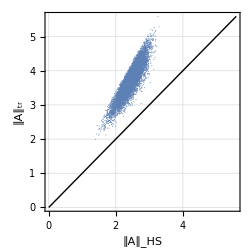

```mathematica
max=Max[data];
ListPlot[data,PlotRange->{{0,1},{0,1}}*max,Epilog->Line@{{0,0},{1,1}*max},FrameLabel->{"∥A∥_HS","∥A∥_tr"},AspectRatio->1]
```

We examine the effects of quantum operations on the Hilbert-Schmidt and trace norms of operators.

We define a function to construct the Kraus elements from the unitary representation of the quantum operation. Here U is the unitary operator on the total system (system plus environment) and init is the initial (pure) state of the environment. The system and environment are assumed to be initially in a product state.

```mathematica
$d=3;
Clear[kraus]
kraus[U_?MatrixQ,init_?VectorQ]:=Map[kraus[U,init,#]&,Range[$d]]
kraus[U_?MatrixQ,init_?VectorQ,k_Integer]:=PartialTrace[
U.CircleTimes[One[$d],Dyad[init,UnitVector[$d,k]]],
{$d,$d},{2}];
```

First, we compare the Hilbert-Schmidt norm before and after quantum operations. Sometimes the Hilbert-Schmidt increases after a quantum operation, especially, for operators with large trace.

```mathematica
EchoTiming[
data=Table[
U=RandomUnitary[$d*$d];
vec=Normalize[RandomVector[$d]];
spr=Supermap[kraus[U,vec]];
mat=RandomReal[{-1,1}]*One[$d]+0.4RandomHermitian[$d];
{HilbertSchmidtNorm[mat],HilbertSchmidtNorm[spr[mat]]},
{10000}
];
]
```

5.48746

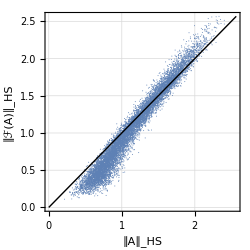

```mathematica
max=Max[data];
ListPlot[data,Epilog->Line@{{0,0},{1,1}*max},
PlotRange->{{0,1},{0,1}}*max,
FrameLabel->{"∥A∥_HS","∥ℱ(A)∥_HS"},
AspectRatio->1]
```

Next, we compare the trace distance before and after quantum operations.

```mathematica
EchoTiming[
data=Table[
U=RandomUnitary[$d*$d];
vec=Normalize[RandomVector[$d]];
spr=Supermap[kraus[U,vec]];
mat=RandomMatrix[$d];
{TraceNorm[mat],TraceNorm[spr[mat]]},
{10000}
];
]
```

4.85604

Unlike the Hilbert-Schmidt norm, the trace norm never increases under a quantum operation.

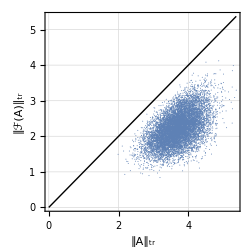

```mathematica
max=Max[data];
ListPlot[data,Epilog->Line@{{0,0},{1,1}*max},
PlotRange->{{0,1},{0,1}}*max,
FrameLabel->{"∥A∥_tr","∥ℱ(A)∥_tr"},
AspectRatio->1]
```

Let us further examine more closely the case for traceless Hermitian operators, which are relevant when investigating the trace distances between mixed states.

```mathematica
EchoTiming[
data=Table[
U=RandomUnitary[$d*$d];
vec=Normalize[RandomVector[$d]];
spr=Supermap[kraus[U,vec]];
mat=RandomHermitian[$d];
mat=mat-Tr[mat]One[$d];
{TraceNorm[mat],TraceNorm[spr[mat]]},
{10000}
];
]
```

6.841

As expected, the trace norm never increases.

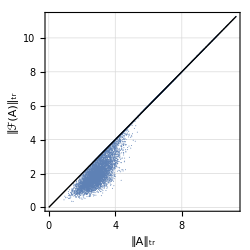

```mathematica
max=Max[data];
ListPlot[data,Epilog->Line@{{0,0},{1,1}*max},
PlotRange->{{0,1},{0,1}}*max,
FrameLabel->{"∥A∥_tr","∥ℱ(A)∥_tr"},
AspectRatio->1]
```

### HIlbert-Schmidt and Trace Distances

Here we demonstrate again that the trace distance never increases under quantum operations, now focusing on quantum states.

```mathematica
EchoTiming[
data=Table[
U=RandomUnitary[$d*$d];
vec=Normalize[RandomVector[$d]];
spr=Supermap[kraus[U,vec]];
rho=RandomPositive[3];rho/=Tr[rho];
sig=RandomPositive[3];sig/=Tr[sig];
{TraceNorm[rho-sig],TraceNorm[spr[rho-sig]]},
{10000}
];
]
```

5.1055

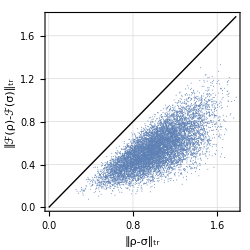

```mathematica
max=Max[data];
ListPlot[data,Epilog->Line@{{0,0},{1,1}*max},
PlotRange->{{0,1},{0,1}}*max,
FrameLabel->{"∥ρ-σ∥_tr","∥ℱ(ρ)-ℱ(σ)∥_tr"},
AspectRatio->1]
```

Let us compare the Hilbert-Schmidt distance between quantum states and the vector-norm-based distance between classical probability distributions.

```mathematica
data=Table[
rho=RandomPositive[3];rho/=Tr[rho];
sig=RandomPositive[3];sig/=Tr[sig];
pp=Chop@Diagonal[rho];
qq=Chop@Diagonal[sig];
{HilbertSchmidtNorm[rho-sig],Norm[pp-qq]},{10000}];
```

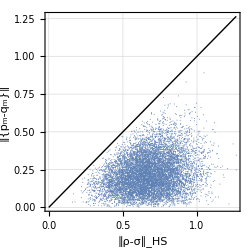

```mathematica
max=Max[data];
ListPlot[data,PlotRange->{{0,1},{0,1}}*max,Epilog->Line@{{0,0},{1,1}*max},FrameLabel->{"∥ρ-σ∥_HS","∥{p_m-q_m}∥"},AspectRatio->1]
```

Let us compare the trace distance between quantum states and the Kolmogorov distance between classical probability distributions.

```mathematica
data=Table[
rho=RandomPositive[3];rho/=Tr[rho];
sig=RandomPositive[3];sig/=Tr[sig];
pp=Chop@Diagonal[rho];
qq=Chop@Diagonal[sig];
{TraceNorm[rho-sig],Total@Abs[pp-qq]},{10000}];
```

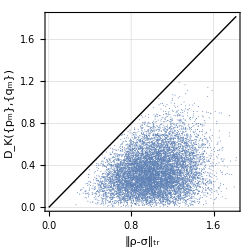

```mathematica
max=Max[data];
ListPlot[data,PlotRange->{{0,1},{0,1}}*max,Epilog->Line@{{0,0},{1,1}*max},FrameLabel->{"∥ρ-σ∥_tr","D_K({p_m},{q_m})"},AspectRatio->1]
```

### Fidelity

Here we demonstrate the non-decreasing feature of the fidelity under quantum operations.

```mathematica
EchoTiming[
data=Chop@Table[
U=RandomUnitary[$d*$d];
vec=Normalize[RandomVector[$d]];
spr=Supermap[kraus[U,vec]];
rho=RandomPositive[3];rho/=Tr[rho];
sig=RandomPositive[3];sig/=Tr[sig];
{Fidelity[rho,sig],Fidelity[spr[rho],spr[sig]]},
{10000}
];
]
```

6.25023

```mathematica
Select[data,First[#]>Last[#]&]
```

{}

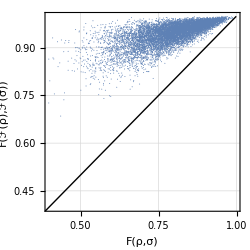

```mathematica
max=Max[data];
min=Min[data];
ListPlot[data,Epilog->Line@{{0,0},{1,1}*max},
PlotRange->{{min,max},{min,max}},
FrameLabel->{"F(ρ,σ)","F(ℱ(ρ),ℱ(σ))"},
AspectRatio->1]
```

Here we compare the fidelity between quantum states and the fidelity between classical probability distributions.

```mathematica
data=Chop@Table[
rho=RandomPositive[3];rho/=Tr[rho];
sig=RandomPositive[3];sig/=Tr[sig];
pp=Chop@Diagonal[rho];
qq=Chop@Diagonal[sig];
{Fidelity[rho,sig],Total@Sqrt[pp*qq]},{10000}];
```

This illustrates that the quantum fidelity is lower than the classical fidelity.

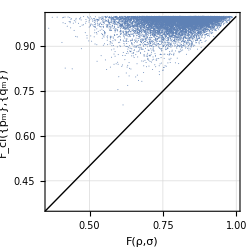

```mathematica
min=Min[data];
max=Max[data];
ListPlot[data,PlotRange->{{min,max},{min,max}},Epilog->Line@{{0,0},{1,1}*max},FrameLabel->{"F(ρ,σ)","F_cl({p_m},{q_m})"},AspectRatio->1]
```